# Inlämningsuppgift 3

Magnus Fredriksson, TIDAB, magfred@kth.se
Fredrik Öberg, TIDAB, fobe@kth.se

Uppgift 1: Trafikflöde

## Sammanfattning

### Uppgift

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett  viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Till exempel om flödet in till en fyrvägs korsning är x_1 fordon/tidsenhet respektive 30 fordon/tidsenhet och flödet ut från korsningen är x_2 fordon/tidsenhet respektive 50 fordon/tidsenhet, så gäller det att x_1+30=x_2+50 eller x_1-x_2=20. Varje korsning ger alltså en linjärekvation i okända flöden x_n. Om man löser ekvationssystemet så kan man bestämma flödet genom trafiksystemet.

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
b) Vilka andra förenklingar har vi antagit?

Studera motorvägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per minut.

c) Ställ upp ekvationssystemet.
d) Bestäm trafikflödet för vägsystemet.
e) Antag att trafiken måste flyta i de riktningar som anges i figuren, vad är då de minsta flödena för x_2, x_3, x_4 och x_5?

figur 1. Trafikflöde i en motorvägskorsning

### Resultat

a)  
 
Antagandet i att trafikflödet bevaras (att bilar in  i korsning = bilar ut ur korsning) är klorrekt om tidsdeltat är oändligt, eller om inflödet stoppas och alla bilar i systemet sedan låts köra ut ur systemet.
Överväg ett scenario där endast en bil finns i systemet, och där systemet bara observeras under en mycket kort period . I detta fall kan bilen bara befinna sig på en av vägarna, vilket skulle får effekten att flödet inte bevaras. betrakta nu systemet, under samma ensamma bils hela färd i systemet, hela bilens väg finns nu dokumenterat, och flödet behålls (såvida bilen inte stannar för evigt i systemet). Samma princip gäller då det finns flera bilar i systemet och att de befinner sig i systemet olika tidslängder, då kommer utflödet inte alltid vara lika med utflöded under en godtycklig tidsperiod. Bilarnas olika hastigheter i systemet kan påverka på liknande sätt.

b)

Det har antagits att in och utflödena ur systemet är lika vilket är en förenkling av verkligheten, enligt exemplet i a). Att alla bilar som kommer in i systemet också kommer att flöda ut ur systemet, vilket inte stämmer då bilar i verkligheten ofta vill komma till en specifik destination (som kan vara inuti systemet). Det har också antagits att strömmen av bilar i systemet är konstant.

c)

k1 = (x2 == 50 +x1)
k2 = (40+x1 ==x3)
k3 = (60+ x6 == x5)
k4 = (x4 == 50+x6)

d)

Trafikflödet i systemet beror på x1 och x6, genom att prova olika värden för x1 och x6 så kan man se flödet för hela systemet.

e)

Funktionen Manipulate användes för att visualisera flödena i sträckorna x2, x3, x4 och x5 över x1 respektive x6.

```mathematica
Manipulate[{x1, x2==50+x1, x3==40+x1},{x1,0,100, 1}]
Manipulate[{x6 , x4==50+x6, x5==60+x6},{x6,0,100, 1}]
```

Funktionerna för x2, x3, x4, och x5 beror på x1 och x6. genom att använda Reduce får man funktionerna för x2, x3, x4, x5. 
x2==50+x1, 
x3==40+x1, 
x4==50+x6, 
x5==60+x6
Man ser att de alla är på formen
flöde = m+Xn 
Där   Xn är antingen x1 eller x6 och m är en konstant. Denna formen ger alltid ett lägre värde då X minskar, eftersom trafikens riktining inte får ändras (ett negativt värde på x1, x6 kan ses som en vändning av trafikens riktning på dessa vägar) så finns alltså de lägsta värdena för alla vägar i systemet då x1 och x6 = 0
 
Då man väljer värde 0 för x1, x6 och inspekterar med Manipulate får man följande resultat: 
		
		x2 = 50
		x3 = 40
		x4 = 50
		x5 = 60 
		
Detta är alltså de minsta flödena.

## Kod

```mathematica
ClearAll["`*"]
```

```mathematica
k1 = (x2 == 50 +x1);
k2 = (40+x1 ==x3);
k3 = (60+ x6 == x5);
k4 = (x4 == 50+x6);
```

```mathematica
reduction = Reduce[{k1, k2, k3, k4},{x2,x3, x4,x5}]
```

x2==50+x1&&x3==40+x1&&x4==50+x6&&x5==60+x6

```mathematica
Manipulate[{x1, x2==50+x1, x3==40+x1},{x1,0,100, 1}];
Manipulate[{x6 , x4==50+x6, x5==60+x6},{x6,0,100, 1}];
```

Uppgift 2: Kaniner

## Sammanfattning

### Uppgift

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

p_(n+2)=p_(n+1)+p_n

Där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

a) Beräkna talföljden och rita en graf över den.
b) Undersök talföljden och diskutera tillväxtakten.
c) Vilka begränsningar har modellen?
d) Hur kan man förbättra modellen?

### Resultat

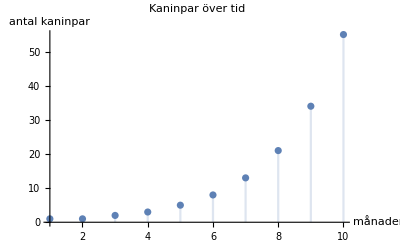
a) 

Talföljden beräknades genom en egenkomponerad funktion och gav oss värdena

	1,1,2,3,5,8,13,21,34,55,89...
	
Grafen över denna talföljd blev som följer:

-Graphics-

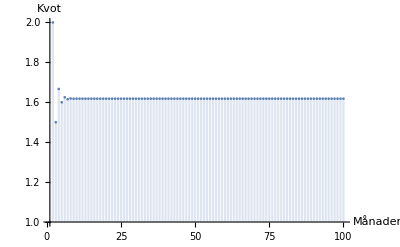
b)

Vi undersökte tillväxttakten genom att visualisera kvoten av på varandra följande värden i följden. 

-Graphics-

Där kan vi se att tillväxten snabbt närmar sig ett konstant värde (~1.6) trots att talen i följden ökar exponentiellt. Vi kan se att kvoten närmar sig vad som kallas det gyllene snittet. Det gyllene snittets proportioner kan man hitta i många av naturens former.  tex  ska växters blad enligt många få en optimal spridning runt stjälken på så sätt att varje blad hamnar på ett ställe där det skuggas minimalt av ovriga blad om de följer det gyllene snittet.  växten ska därmed kunna utnyttja ljuset optimalt. Det här påståendet är dock inte bevisat.

c)

Modellen tar inte hänsyn till att kaniner dör efter ett tag.  Även verkliga aspekter som att en art som förökar sig oändligt kommer att få slut på resurser i form av mat och vatten. Kaninerna kommer också uppleva dålig hygien på grund av brist på utrymme som i sin tur påverkar populationsnivån negativt. Bristen på utrymme kan till och med leda till en utrotad befolkning. Modellen är helt enkelt inte realistisk; allteftersom tiden går når kaninpopulationen sådanna storlekar att den inte skulle få plats i universum.

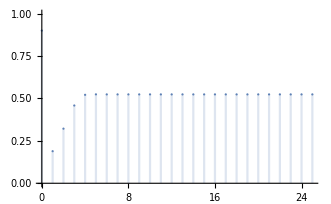
d)

Vi skulle kunna ta hänsyn till att kaninerna har begränsad livslängd. Det skulle kunna göras genom att lägga in det i funktionen, så¨här:

funktion(x) = funktion(x-1) +  funktion(x-2) - funktion(x-livslängd)

Faktorer som resurser och utrymme skulle också kunna läggas in i modellen för att få ett mer verklighetsbaserat resultat.
Det finns en välkänd formel som använts inom biologi för att föruspå tillväxten  i denna funktionen får man ut artens storlek mellan 0-1 efter x år, där 1 motsvarar maximal storlek och 0 är 0. Modellen ser ut så här
[Logistic map, wikipedia]

storlek(x+1) = fertilitet * storlek(x)*(1-storlek(x)  

Så här ser denna funktionen ut då den initiala storleken är 0.1 och fertiliteten 2.3.


 -Graphics-
 Efter ett antal år kan denna funktionen antingen balansera ut sig, d.v.s. att storleken är samma år efter år, eller resultera i en cykel av storlekar som varierar mellan  2^n värden, beroende på hur hög fertiliteten är.
 [The Feigenbaum Constant (4.669) - Numberphile , youtube.com]

## Kod

```mathematica
ClearAll["`*"]
```

En rekursiv funktion definieras för kaninparens tillväxt. Stoppkriterier för rekursioner finns då x = 1, x = 2

```mathematica
rabbits[x_]:=rabbits[x]=rabbits[x-1]+rabbits[x-2];
rabbits[1]= 1;
rabbits[2] = 1;
rabbitsOverTime = DiscretePlot[{rabbits[x]}, {x,1,10,1}, PlotStyle->Join,
 AxesLabel->{"månader","antal kaninpar"},
PlotLabel->"Kaninpar över tid"];
Show[{rabbitsOverTime}]
```

-Graphics-

En funktion för kvoten mellan två på varandra följande kaninparsvärden

```mathematica
xV = 100;
DiscretePlot[{rabbits[x+1]/rabbits[x]}, {x, 1,xV}, PlotRange-> {{1, xV},{1,2}},
AxesLabel-> {"Månader", "Kvot"}]
```

-Graphics-

En alternativ funktion för en populations tillväxt görs.

```mathematica
fertility =2.3;
startPopulation = 0.1;
advancedPopulation[x_] := advancedPopulation[x] = fertility*advancedPopulation[x-1]*(1-advancedPopulation[x-1]);   
advancedPopulation[0] = startPopulation; 
xMax = 25;
DiscretePlot[{advancedPopulation[x]}, {x, 0,xMax}, PlotRange-> {{0, xMax},{0,1}}];
```